```mathematica
Fmajor[qx_,qz_]:=x0/λr*Sin[w[qx,qz]]/w[qx,qz]
Fminor[qx_,qz_]:=f1*(λr-x0)/λr*Cos[0.5(0.5qx λr+w[qx,qz])]/Cos[0.5(0.5qx λr-w[qx,qz])]*Sin[0.5qx λr-w[qx,qz]]/(0.5qx λr-w[qx,qz])
Fkink[qx_,qz_]:=f2*2*Cos[w[qx,qz]]/λr
w[qx_,qz_]:=0.5(qx x0+qz A)
x0=103;
A=21.5;
λr=145;
f1=0.5;
f2=-3;
xmin=-0.3;xmax=0.3;
zmin=0;zmax=1.1;
output=Partition[Flatten[Table[{qx,qz,Abs[Fmajor[qx,qz]]},{qx,xmin,xmax,0.005},{qz,zmin,zmax,0.005}]],3];
Export["~/documents/thesis/figures/ripple/model/FTmajor.dat",output]
output=Partition[Flatten[Table[{qx,qz,Abs[Fmajor[qx,qz]+Fminor[qx,qz]+Fkink[qx,qz]]},{qx,xmin,xmax,0.005},{qz,zmin,zmax,0.005}]],3];
Export["~/documents/thesis/figures/ripple/model/FT.dat",output]
(*ContourPlot[Abs[Fmajor[x,z]],{x,xmin,xmax},{z,zmin,zmax},Contours->20,AspectRatio->Automatic]
ContourPlot[Abs[Fminor[x,z]],{x,xmin,xmax},{z,zmin,zmax},Contours->20,AspectRatio->Automatic]
ContourPlot[Abs[Fkink[x,z]],{x,xmin,xmax},{z,zmin,zmax},Contours->20,AspectRatio->Automatic]*)
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

~/documents/thesis/figures/ripple/model/FTmajor.dat

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

~/documents/thesis/figures/ripple/model/FT.dat

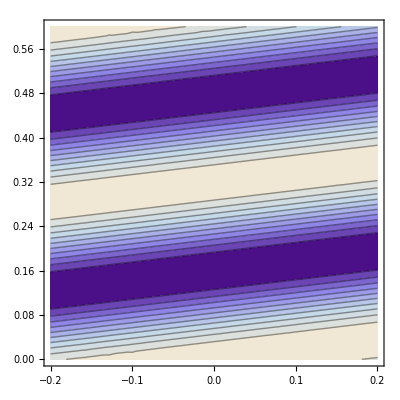

```mathematica
FT[qx_,qz_]:=RHM Cos[qz Xh Cos[ψ]-qx Xh Sin[ψ]]-1
ψ=10*π/180;
RHM=2.2;
Xh=20;
xmin=-0.2;xmax=0.2;
zmin=0;zmax=0.6;
ContourPlot[FT[x,z],{x,xmin,xmax},{z,zmin,zmax},Contours->10]
```

```mathematica
func[i_,j_]:=i+j
Export["~/test.dat",Table[{i,j,func[i,j]},{j,0,2,1}]]
```

~/test.dat

```mathematica
For[i=0,i<4,i++,Table[{i,j,func[i,j]},{j,0,2,1}]]
```

```mathematica
i=0;
Table[{i,j,func[i,j]},{j,0,2,1}]
```

{{0,0,0},{0,1,1},{0,2,2}}

```mathematica
output=Partition[Flatten[Table[{i,j,func[i,j]},{i,0,3,1},{j,0,3,1}]],3];
Export["~/test.dat",output]
```

~/test.dat